```mathematica
data=Cases[Import["/Users/kirillivanov/Documents/Лабы/3.4.2.xlsx"]⟦1,All,2;;⟧,Except[{"Таблица 1"|"",""..}]]
```

{{,T_в,dU,T_o,\sigmaT,\tau,Tdif,Trev,\sigmadif,\sigmarev},{1.,14.23,0.001,14.25,0.104065,7.937,14.605,0.068,0.159,0.001},{2.,16.12,-0.017,15.71,0.104065,7.872,13.577,0.074,0.157,0.001},{3.,18.12,-0.018,17.69,0.104065,7.755,11.749,0.085,0.155,0.001},{4.,20.1,-0.018,19.67,0.104065,7.568,8.884,0.113,0.151,0.002},{5.,22.1,-0.017,21.69,0.104065,7.358,5.749,0.174,0.147,0.004},{6.,24.11,-0.018,23.68,0.104065,7.193,3.348,0.299,0.144,0.013},{7.,26.08,-0.018,25.65,0.104065,7.121,2.318,0.431,0.142,0.027},{8.,28.1,-0.012,27.81,0.104065,7.079,1.721,0.581,0.142,0.048},{9.,30.09,-0.017,29.68,0.104065,7.055,1.382,0.724,0.141,0.074},{10.,32.08,-0.018,31.65,0.104065,7.036,1.114,0.897,0.141,0.113},{11.,34.08,-0.017,33.67,0.104065,7.022,0.918,1.09,0.14,0.13},{12.,36.09,-0.019,35.63,0.104065,7.013,0.791,1.264,0.14,0.152},{13.,38.08,-0.018,37.65,0.104065,7.005,0.679,1.473,0.14,0.185},{14.,40.08,-0.019,39.62,0.104065,6.999,0.595,1.681,0.14,0.211}}

```mathematica
{{"Tаблица 1" ,"","","","","",""},{"","","","","","",""},{"","T_в","dU","T_o","\\tau","",""},{1.,14.23,0.,14.23,7.937,14.6050245504,0.06846958706225605},{2.,16.12,-0.017,15.712,7.872,13.5774395504,0.07365158918866549},{3.,18.12,-0.018,17.688,7.755,11.7490805504,0.08511304316199914},{4.,20.1,-0.018,19.668,7.568,8.883679550399997,0.1125659693516268},{5.,22.1,-0.017,21.692,7.358,5.749219550399992,0.1739366519635568},{6.,24.11,-0.018,23.678,7.193,3.348304550399995,0.2986586151132931},{7.,26.08,-0.018,25.648,7.121,2.317696550400008,0.431462867659449},{8.,28.1,-0.012,27.812,7.079,1.721296550399998,0.5809574182714873},{9.,30.09,-0.017,29.682,7.055,1.382080550399998,0.7235468292427549},{10.,32.08,-0.018,31.648,7.036,1.114351550399995,0.8973828767421298},{11.,34.08,-0.017,33.672,7.022,0.9175395504000008,1.089871275373417},{12.,36.09,-0.019,35.634,7.013,0.7912245504000026,1.263863715419916},{13.,38.08,-0.018,37.648,7.005,0.6790805504000019,1.472579356618247},{14.,40.08,-0.019,39.624,6.999,0.5950565503999954,1.680512548475944},{"","","","","","",""},{"","","","","","",""},{"","","","","","",""},{"","","","","","",""},{"","","","","","",""},{"","","","","","",""}}
```

```mathematica
dat=Cases[Import["/Users/kirillivanov/Documents/Лабы/3.4.2.xlsx"]⟦1,All,2;;⟧,Except[{"Таблица 1"|"",""..}]]
TableForm@dat
```

{{,\sigmaT,\sigmadif,\sigmarev},{1.,0.104065,0.159,0.001},{2.,0.104065,0.157,0.001},{3.,0.104065,0.155,0.001},{4.,0.104065,0.151,0.002},{5.,0.104065,0.147,0.004},{6.,0.104065,0.144,0.013},{7.,0.104065,0.142,0.027},{8.,0.104065,0.142,0.048},{9.,0.104065,0.141,0.074},{10.,0.104065,0.141,0.113},{11.,0.104065,0.14,0.13},{12.,0.104065,0.14,0.152},{13.,0.104065,0.14,0.185},{14.,0.104065,0.14,0.211}}

```mathematica
dat //TableForm
```

```mathematica
{{"", "\\sigmaT", "\\sigmadif", "\\sigmarev"}, {1., 0.10406459532425, 0.159, 0.001}, {2., 0.10406459532425, 0.157, 0.001}, {3., 0.10406459532425, 0.155, 0.001}, {4., 0.10406459532425, 0.151, 0.002}, {5., 0.10406459532425, 0.147, 0.004}, {6., 0.10406459532425, 0.144, 0.013}, {7., 0.10406459532425, 0.142, 0.027}, {8., 0.10406459532425, 0.142, 0.048}, {9., 0.10406459532425, 0.141, 0.074}, {10., 0.10406459532425, 0.141, 0.113}, {11., 0.10406459532425, 0.14, 0.13}, {12., 0.10406459532425, 0.14, 0.152}, {13., 0.10406459532425, 0.14, 0.185}, {14., 0.10406459532425, 0.14, 0.211}}
dat//TeXForm
```

{{,\sigmaT,\sigmadif,\sigmarev},{1.,0.104065,0.159,0.001},{2.,0.104065,0.157,0.001},{3.,0.104065,0.155,0.001},{4.,0.104065,0.151,0.002},{5.,0.104065,0.147,0.004},{6.,0.104065,0.144,0.013},{7.,0.104065,0.142,0.027},{8.,0.104065,0.142,0.048},{9.,0.104065,0.141,0.074},{10.,0.104065,0.141,0.113},{11.,0.104065,0.14,0.13},{12.,0.104065,0.14,0.152},{13.,0.104065,0.14,0.185},{14.,0.104065,0.14,0.211}}

\left(
\begin{array}{cccc}
 \text{} & \text{$\backslash \backslash $sigmaT} & \text{$\backslash \backslash $sigmadif} & \text{$\backslash \backslash $sigmarev} \\
 1. & 0.104065 & 0.159 & 0.001 \\
 2. & 0.104065 & 0.157 & 0.001 \\
 3. & 0.104065 & 0.155 & 0.001 \\
 4. & 0.104065 & 0.151 & 0.002 \\
 5. & 0.104065 & 0.147 & 0.004 \\
 6. & 0.104065 & 0.144 & 0.013 \\
 7. & 0.104065 & 0.142 & 0.027 \\
 8. & 0.104065 & 0.142 & 0.048 \\
 9. & 0.104065 & 0.141 & 0.074 \\
 10. & 0.104065 & 0.141 & 0.113 \\
 11. & 0.104065 & 0.14 & 0.13 \\
 12. & 0.104065 & 0.14 & 0.152 \\
 13. & 0.104065 & 0.14 & 0.185 \\
 14. & 0.104065 & 0.14 & 0.211 \\
\end{array}
\right)

```mathematica
tauDiff=data⟦All,{4,6}⟧
tauDiffReverse=data⟦All,{4,7}⟧
```

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
```

```mathematica
data//TeXForm
```

\left(
\begin{array}{cccccccccc}
 \text{} & \text{T$\_\unicode{0432}$} & \text{dU} & \text{T$\_$o} & \text{$\backslash \backslash $sigmaT} & \text{$\backslash \backslash $tau} &
   \text{Tdif} & \text{Trev} & \text{$\backslash \backslash $sigmadif} & \text{$\backslash \backslash $sigmarev} \\
 1. & 14.23 & 0.001 & 14.25 & 0.104065 & 7.937 & 14.605 & 0.068 & 0.159 & 0.001 \\
 2. & 16.12 & -0.017 & 15.71 & 0.104065 & 7.872 & 13.577 & 0.074 & 0.157 & 0.001 \\
 3. & 18.12 & -0.018 & 17.69 & 0.104065 & 7.755 & 11.749 & 0.085 & 0.155 & 0.001 \\
 4. & 20.1 & -0.018 & 19.67 & 0.104065 & 7.568 & 8.884 & 0.113 & 0.151 & 0.002 \\
 5. & 22.1 & -0.017 & 21.69 & 0.104065 & 7.358 & 5.749 & 0.174 & 0.147 & 0.004 \\
 6. & 24.11 & -0.018 & 23.68 & 0.104065 & 7.193 & 3.348 & 0.299 & 0.144 & 0.013 \\
 7. & 26.08 & -0.018 & 25.65 & 0.104065 & 7.121 & 2.318 & 0.431 & 0.142 & 0.027 \\
 8. & 28.1 & -0.012 & 27.81 & 0.104065 & 7.079 & 1.721 & 0.581 & 0.142 & 0.048 \\
 9. & 30.09 & -0.017 & 29.68 & 0.104065 & 7.055 & 1.382 & 0.724 & 0.141 & 0.074 \\
 10. & 32.08 & -0.018 & 31.65 & 0.104065 & 7.036 & 1.114 & 0.897 & 0.141 & 0.113 \\
 11. & 34.08 & -0.017 & 33.67 & 0.104065 & 7.022 & 0.918 & 1.09 & 0.14 & 0.13 \\
 12. & 36.09 & -0.019 & 35.63 & 0.104065 & 7.013 & 0.791 & 1.264 & 0.14 & 0.152 \\
 13. & 38.08 & -0.018 & 37.65 & 0.104065 & 7.005 & 0.679 & 1.473 & 0.14 & 0.185 \\
 14. & 40.08 & -0.019 & 39.62 & 0.104065 & 6.999 & 0.595 & 1.681 & 0.14 & 0.211 \\
\end{array}
\right)

```mathematica
TableForm@dat
```

| T_в | dU | T_o | \sigmaT | \tau | Tdif | Trev | \sigmadif | \sigmarev
1. | 14.23 | 0.001 | 14.25 | 0.104065 | 7.937 | 14.605 | 0.068 | 0.159 | 0.001
2. | 16.12 | -0.017 | 15.71 | 0.104065 | 7.872 | 13.577 | 0.074 | 0.157 | 0.001
3. | 18.12 | -0.018 | 17.69 | 0.104065 | 7.755 | 11.749 | 0.085 | 0.155 | 0.001
4. | 20.1 | -0.018 | 19.67 | 0.104065 | 7.568 | 8.884 | 0.113 | 0.151 | 0.002
5. | 22.1 | -0.017 | 21.69 | 0.104065 | 7.358 | 5.749 | 0.174 | 0.147 | 0.004
6. | 24.11 | -0.018 | 23.68 | 0.104065 | 7.193 | 3.348 | 0.299 | 0.144 | 0.013
7. | 26.08 | -0.018 | 25.65 | 0.104065 | 7.121 | 2.318 | 0.431 | 0.142 | 0.027
8. | 28.1 | -0.012 | 27.81 | 0.104065 | 7.079 | 1.721 | 0.581 | 0.142 | 0.048
9. | 30.09 | -0.017 | 29.68 | 0.104065 | 7.055 | 1.382 | 0.724 | 0.141 | 0.074
10. | 32.08 | -0.018 | 31.65 | 0.104065 | 7.036 | 1.114 | 0.897 | 0.141 | 0.113
11. | 34.08 | -0.017 | 33.67 | 0.104065 | 7.022 | 0.918 | 1.09 | 0.14 | 0.13
12. | 36.09 | -0.019 | 35.63 | 0.104065 | 7.013 | 0.791 | 1.264 | 0.14 | 0.152
13. | 38.08 | -0.018 | 37.65 | 0.104065 | 7.005 | 0.679 | 1.473 | 0.14 | 0.185
14. | 40.08 | -0.019 | 39.62 | 0.104065 | 6.999 | 0.595 | 1.681 | 0.14 | 0.211

```mathematica
Needs@"ErrorBarPlots`";
vertSize=0.15;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

```mathematica
errorListPlot[numbersData_]:=ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dat⟦2;;,numbersData⟧,
GridLines->{grids@1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"T_o, °C","τ^2-τ_0^2, (:043c:043a:0441)^2"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)}],
PlotMarkers->{Automatic,0.01},Joined->True,PlotStyle->Thickness@0.004,
PlotRange->{{11,43}, Automatic},
ImageSize->1000]
(*Export[FileNameJoin@{NotebookDirectory[],"dif.png"},%]*)
```

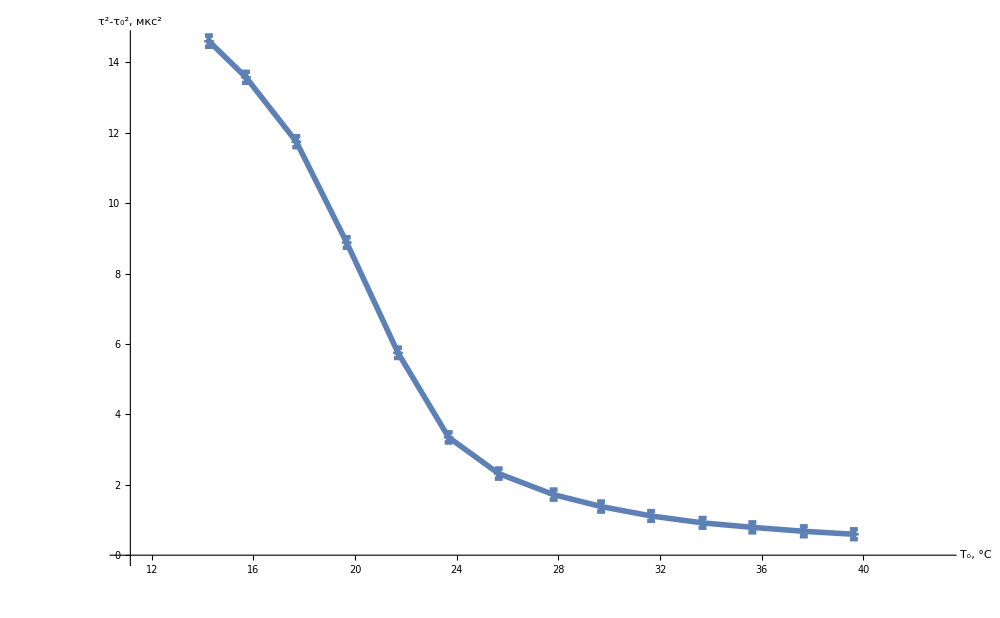

```mathematica
errorListPlot@{4,7,5,9}
```

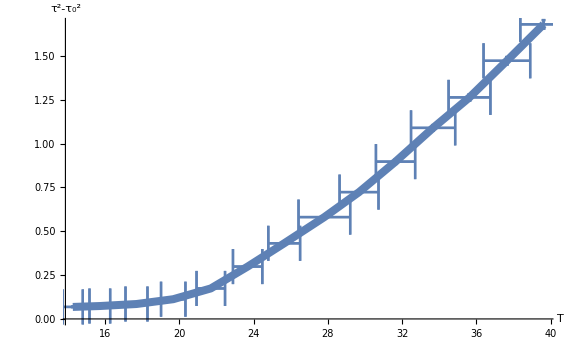

```mathematica
errorListPlot@{4,9,5,10}
```

```mathematica
forFit=Select[dat⟦2;;,{4,8,5,10}⟧,First@#>22&];
```

```mathematica
fit=LinearModelFit[forFit⟦All,;;2⟧,{1,x},x];
fit@"ParameterTable"
fit@Function
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.81676 | 0.0816537 | -22.2496 | 9.36572×10^-8
x | 0.0869733 | 0.0025449 | 34.1755 | 4.761×10^-9

-1.81676+0.0869733 Function

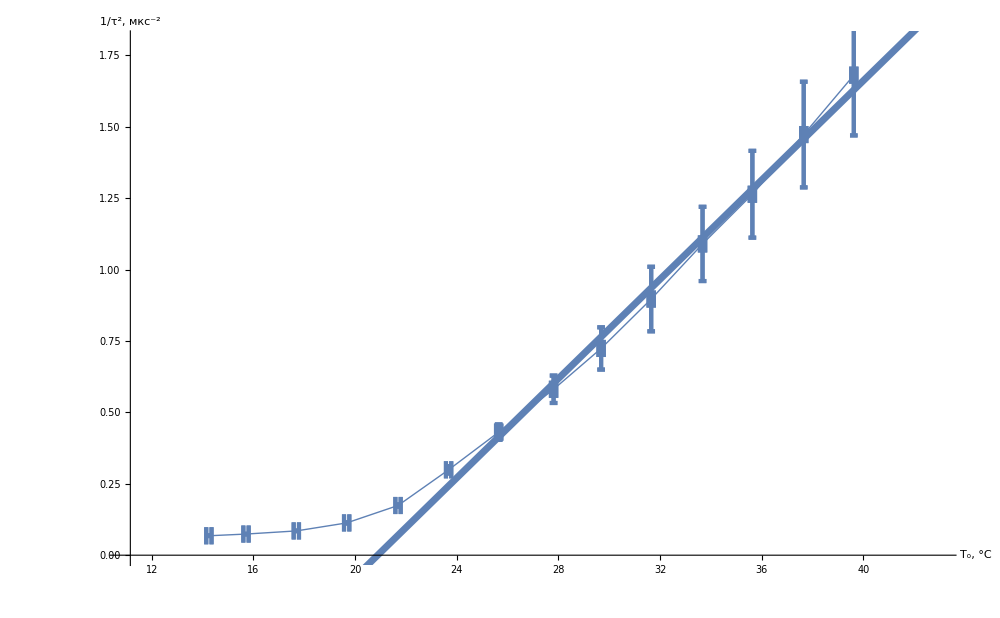

/Users/kirillivanov/Documents/Лабы/reverse.png

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dat⟦2;;,{4,8,5,10}⟧,
GridLines->{grids@1,grids@0.2},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"T_o, °C","1/τ^2, (:043c:043a:0441)^-2"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)}],
PlotMarkers->{Automatic,0.01},Joined->True,PlotStyle->Thickness@0.001,
PlotRange->{{11,43},{0,1.8}},
ImageSize->1000],Plot[fit["Function"]@x,{x,20,45}, PlotStyle->Thickness@0.005]]
Export[FileNameJoin@{NotebookDirectory[],"reverse.png"},%]
```

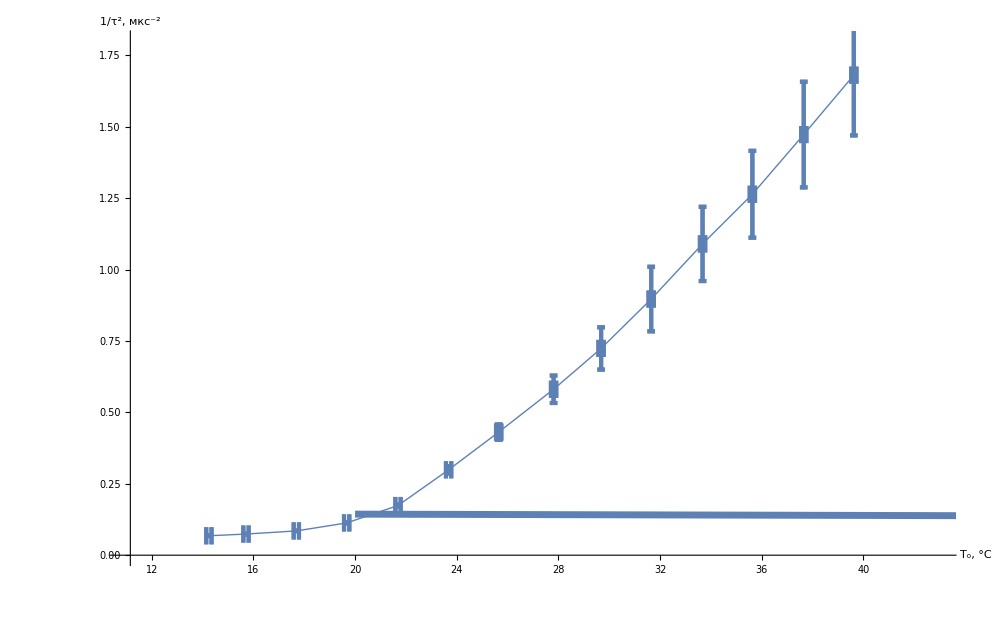

/Users/kirillivanov/Documents/Лабы/reverse.png

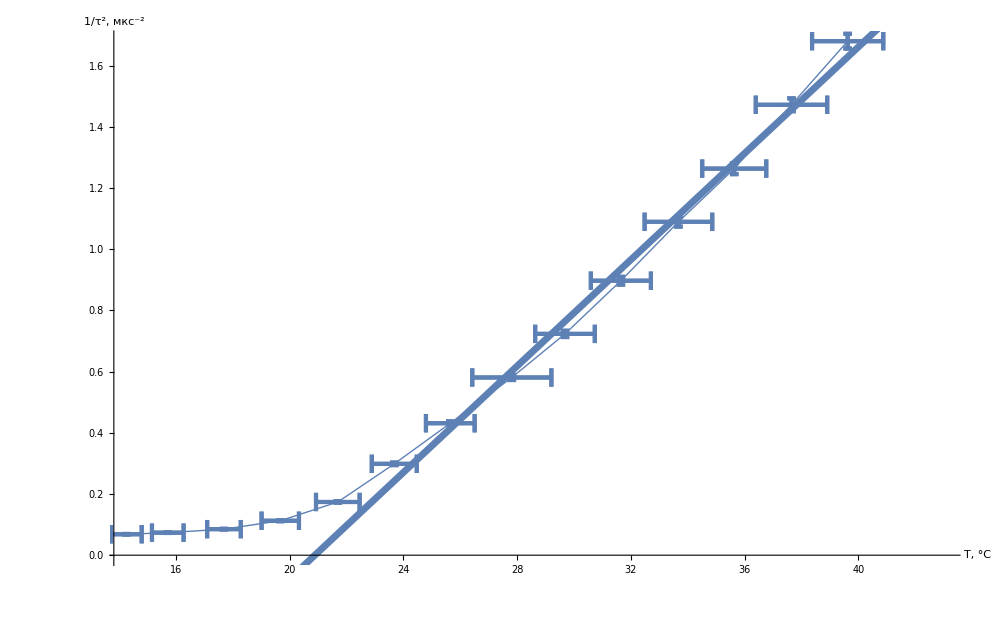

/Users/kirillivanov/Documents/Лабы/reverse.png

```mathematica
Prepend[Round[1000Rest@data]/1000.,First@data]//TeXForm
```

\left(
\begin{array}{cccccccccc}
 \text{} & \text{T$\_\unicode{0432}$} & \text{dU} & \text{T$\_$o} & \text{sigmaT$\_$o} & \text{$\backslash \backslash $tau} & \text{tDiff} &
   \text{sigmatDiff} & \text{tDiffRev} & \text{sigmatDiffRev} \\
 1. & 14.23 & 0.001 & 14.254 & 0.54 & 7.937 & 14.605 & 0.184 & 0.068 & 0.001 \\
 2. & 16.12 & -0.017 & 15.712 & 0.557 & 7.872 & 13.577 & 0.172 & 0.074 & 0.001 \\
 3. & 18.12 & -0.018 & 17.688 & 0.592 & 7.755 & 11.749 & 0.152 & 0.085 & 0.001 \\
 4. & 20.1 & -0.018 & 19.668 & 0.657 & 7.568 & 8.884 & 0.117 & 0.113 & 0.001 \\
 5. & 22.1 & -0.017 & 21.692 & 0.767 & 7.358 & 5.749 & 0.078 & 0.174 & 0.002 \\
 6. & 24.11 & -0.018 & 23.678 & 0.791 & 7.193 & 3.348 & 0.047 & 0.299 & 0.004 \\
 7. & 26.08 & -0.018 & 25.648 & 0.856 & 7.121 & 2.318 & 0.033 & 0.431 & 0.006 \\
 8. & 28.1 & -0.012 & 27.812 & 1.391 & 7.079 & 1.721 & 0.024 & 0.581 & 0.008 \\
 9. & 30.09 & -0.017 & 29.682 & 1.049 & 7.055 & 1.382 & 0.02 & 0.724 & 0.01 \\
 10. & 32.08 & -0.018 & 31.648 & 1.056 & 7.036 & 1.114 & 0.016 & 0.897 & 0.013 \\
 11. & 34.08 & -0.017 & 33.672 & 1.189 & 7.022 & 0.918 & 0.013 & 1.09 & 0.016 \\
 12. & 36.09 & -0.019 & 35.634 & 1.126 & 7.013 & 0.791 & 0.011 & 1.264 & 0.018 \\
 13. & 38.08 & -0.018 & 37.648 & 1.256 & 7.005 & 0.679 & 0.01 & 1.473 & 0.021 \\
 14. & 40.08 & -0.019 & 39.624 & 1.252 & 6.999 & 0.595 & 0.009 & 1.681 & 0.024 \\
\end{array}
\right)

```mathematica
data1=Cases[Import["/Users/kirillivanov/Documents/Лабы/3.4.2.xlsx"]⟦1,All,2;;⟧,Except[{"Таблица 1"|"",""..}]]
```

{{,T_в,dU,T_o,\tau,tDiff,tDiffRev},{1.,14.23,0.001,14.254,7.937,14.605,0.0684696},{2.,16.12,-0.017,15.712,7.872,13.5774,0.0736516},{3.,18.12,-0.018,17.688,7.755,11.7491,0.085113},{4.,20.1,-0.018,19.668,7.568,8.88368,0.112566},{5.,22.1,-0.017,21.692,7.358,5.74922,0.173937},{6.,24.11,-0.018,23.678,7.193,3.3483,0.298659},{7.,26.08,-0.018,25.648,7.121,2.3177,0.431463},{8.,28.1,-0.012,27.812,7.079,1.7213,0.580957},{9.,30.09,-0.017,29.682,7.055,1.38208,0.723547},{10.,32.08,-0.018,31.648,7.036,1.11435,0.897383},{11.,34.08,-0.017,33.672,7.022,0.91754,1.08987},{12.,36.09,-0.019,35.634,7.013,0.791225,1.26386},{13.,38.08,-0.018,37.648,7.005,0.679081,1.47258},{14.,40.08,-0.019,39.624,6.999,0.595057,1.68051}}

```mathematica
data1//TableForm
Prepend[Round[1000Rest@data1]/1000.,First@data1]//TeXForm
```

| T_в | dU | T_o | \tau | tDiff | tDiffRev
1. | 14.23 | 0.001 | 14.254 | 7.937 | 14.605 | 0.0684696
2. | 16.12 | -0.017 | 15.712 | 7.872 | 13.5774 | 0.0736516
3. | 18.12 | -0.018 | 17.688 | 7.755 | 11.7491 | 0.085113
4. | 20.1 | -0.018 | 19.668 | 7.568 | 8.88368 | 0.112566
5. | 22.1 | -0.017 | 21.692 | 7.358 | 5.74922 | 0.173937
6. | 24.11 | -0.018 | 23.678 | 7.193 | 3.3483 | 0.298659
7. | 26.08 | -0.018 | 25.648 | 7.121 | 2.3177 | 0.431463
8. | 28.1 | -0.012 | 27.812 | 7.079 | 1.7213 | 0.580957
9. | 30.09 | -0.017 | 29.682 | 7.055 | 1.38208 | 0.723547
10. | 32.08 | -0.018 | 31.648 | 7.036 | 1.11435 | 0.897383
11. | 34.08 | -0.017 | 33.672 | 7.022 | 0.91754 | 1.08987
12. | 36.09 | -0.019 | 35.634 | 7.013 | 0.791225 | 1.26386
13. | 38.08 | -0.018 | 37.648 | 7.005 | 0.679081 | 1.47258
14. | 40.08 | -0.019 | 39.624 | 6.999 | 0.595057 | 1.68051

\left(
\begin{array}{ccccccc}
 \text{} & \text{T$\_\unicode{0432}$} & \text{dU} & \text{T$\_$o} & \text{$\backslash \backslash $tau} & \text{tDiff} & \text{tDiffRev} \\
 1. & 14.23 & 0.001 & 14.254 & 7.937 & 14.605 & 0.068 \\
 2. & 16.12 & -0.017 & 15.712 & 7.872 & 13.577 & 0.074 \\
 3. & 18.12 & -0.018 & 17.688 & 7.755 & 11.749 & 0.085 \\
 4. & 20.1 & -0.018 & 19.668 & 7.568 & 8.884 & 0.113 \\
 5. & 22.1 & -0.017 & 21.692 & 7.358 & 5.749 & 0.174 \\
 6. & 24.11 & -0.018 & 23.678 & 7.193 & 3.348 & 0.299 \\
 7. & 26.08 & -0.018 & 25.648 & 7.121 & 2.318 & 0.431 \\
 8. & 28.1 & -0.012 & 27.812 & 7.079 & 1.721 & 0.581 \\
 9. & 30.09 & -0.017 & 29.682 & 7.055 & 1.382 & 0.724 \\
 10. & 32.08 & -0.018 & 31.648 & 7.036 & 1.114 & 0.897 \\
 11. & 34.08 & -0.017 & 33.672 & 7.022 & 0.918 & 1.09 \\
 12. & 36.09 & -0.019 & 35.634 & 7.013 & 0.791 & 1.264 \\
 13. & 38.08 & -0.018 & 37.648 & 7.005 & 0.679 & 1.473 \\
 14. & 40.08 & -0.019 & 39.624 & 6.999 & 0.595 & 1.681 \\
\end{array}
\right)

```mathematica
datap=Cases[Import["/Users/kirillivanov/Documents/Лабы/3.4.2.xlsx"]⟦1,All,2;;⟧,Except[{"Таблица 1"|"",""..}]]
```

{{,\sigmaT,\sigmadif,\sigmarev},{1.,0.104065,0.159,0.001},{2.,0.104065,0.157,0.001},{3.,0.104065,0.155,0.001},{4.,0.104065,0.151,0.002},{5.,0.104065,0.147,0.004},{6.,0.104065,0.144,0.013},{7.,0.104065,0.142,0.027},{8.,0.104065,0.142,0.048},{9.,0.104065,0.141,0.074},{10.,0.104065,0.141,0.113},{11.,0.104065,0.14,0.13},{12.,0.104065,0.14,0.152},{13.,0.104065,0.14,0.185},{14.,0.104065,0.14,0.211}}

```mathematica
datap//TableForm
Prepend[Round[1000Rest@datap]/1000.,First@datap]//TeXForm
```

| \sigmaT | \sigmadif | \sigmarev
1. | 0.104065 | 0.159 | 0.001
2. | 0.104065 | 0.157 | 0.001
3. | 0.104065 | 0.155 | 0.001
4. | 0.104065 | 0.151 | 0.002
5. | 0.104065 | 0.147 | 0.004
6. | 0.104065 | 0.144 | 0.013
7. | 0.104065 | 0.142 | 0.027
8. | 0.104065 | 0.142 | 0.048
9. | 0.104065 | 0.141 | 0.074
10. | 0.104065 | 0.141 | 0.113
11. | 0.104065 | 0.14 | 0.13
12. | 0.104065 | 0.14 | 0.152
13. | 0.104065 | 0.14 | 0.185
14. | 0.104065 | 0.14 | 0.211

\left(
\begin{array}{cccc}
 \text{} & \text{$\backslash \backslash $sigmaT} & \text{$\backslash \backslash $sigmadif} & \text{$\backslash \backslash $sigmarev} \\
 1. & 0.104 & 0.159 & 0.001 \\
 2. & 0.104 & 0.157 & 0.001 \\
 3. & 0.104 & 0.155 & 0.001 \\
 4. & 0.104 & 0.151 & 0.002 \\
 5. & 0.104 & 0.147 & 0.004 \\
 6. & 0.104 & 0.144 & 0.013 \\
 7. & 0.104 & 0.142 & 0.027 \\
 8. & 0.104 & 0.142 & 0.048 \\
 9. & 0.104 & 0.141 & 0.074 \\
 10. & 0.104 & 0.141 & 0.113 \\
 11. & 0.104 & 0.14 & 0.13 \\
 12. & 0.104 & 0.14 & 0.152 \\
 13. & 0.104 & 0.14 & 0.185 \\
 14. & 0.104 & 0.14 & 0.211 \\
\end{array}
\right)

```mathematica
ClearAll@"Global`*"

dat //TableForm
```

```mathematica
dat // TableForm
```

dat